# MS-C1650 - Numerical Analysis Week 19: Lecture 8: Gauss Quadratures

## Harri Hakula, 2021

## Gauss

```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
polys=Table[Function[x,Evaluate[x^k],Listable],{k,0,40}];
```

```mathematica
n=5
```

5

```mathematica
{q,w}=Transpose[GaussianQuadratureWeights[n,-1,1]]
```

{{-0.90618,-0.538469,0.,0.538469,0.90618},{0.236927,0.478629,0.568889,0.478629,0.236927}}

```mathematica
error=Table[{Exponent[p[x],x],Chop[Integrate[p[x],{x,-1,1}]-w.p[q]]},{p,polys}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0.00293181},{11,0},{12,0.00799357},{13,0},{14,0.0138669},{15,0},{16,0.0196334},{17,0},{18,0.0248035},{19,0},{20,0.029175},{21,0},{22,0.0327102},{23,0},{24,0.0354556},{25,0},{26,0.0374961},{27,0},{28,0.0389291},{29,0},{30,0.0398514},{31,0},{32,0.0403523},{33,0},{34,0.0405113},{35,0},{36,0.0403968},{37,0},{38,0.0400673},{39,0},{40,0.0395713}}

## Gauss Point Distribution

```mathematica
n=5;
{q,w}=Transpose[GaussianQuadratureWeights[n,-1,1]]
```

{{-0.90618,-0.538469,0.,0.538469,0.90618},{0.236927,0.478629,0.568889,0.478629,0.236927}}

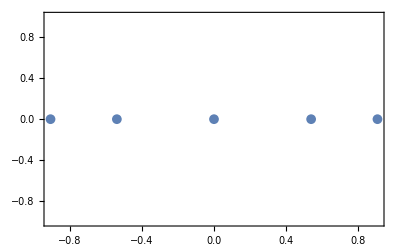

```mathematica
ListPlot[Thread[List[q,0]],PlotMarkers->{Automatic, Medium},Frame->True]
```

```mathematica
n=15;
{q,w}=Transpose[GaussianQuadratureWeights[n,-1,1]];
```

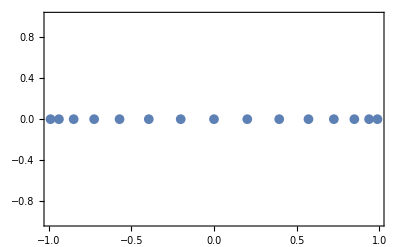

```mathematica
ListPlot[Thread[List[q,0]],PlotMarkers->{Automatic, Medium},Frame->True]
```